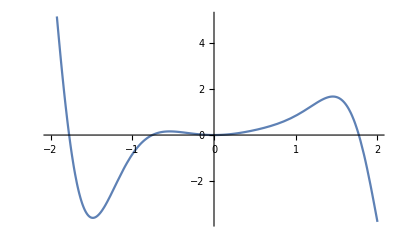

```mathematica
(*Зададим данную функцию и построим ее график*)
f[x_]=(x^3-x^2+1)*Sin[x^2];
Plot[f[x],{x,-2,2}]
```

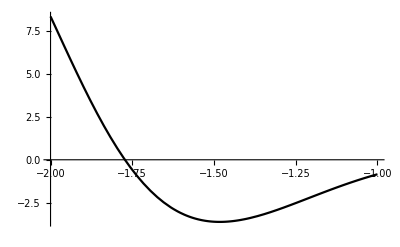

```mathematica
(*Локализуем точку экстремума данной функции*)
A=-2;
B=-1;
G=Plot[f[x],{x,A,B},PlotStyle->Black]
```

```mathematica
(*Найдем точку экстремума методом равномерного приближения*)
(*Зададим точность*)
ϵ=10^(-5);
(*Зададим отрезок унимодальности функции*)
a=A;
b=B;
(*Зададим параметр, описывающий характер точки экстремума.
Если 1, то точка экстремума - точка минимума.
Если -1, то точка экстремума - точка максимума*)
M=1;
(*Зададим вспомогательную функцию для поиска точки минимума*)
g[x_]=M*f[x];
(*Найдем количество частичных отрезков*)
n=Floor[(b-a)/ϵ]+1;
(*Зададим шаг разбиения отрезка унимодальности*)
h=(b-a)/n;
(*Зададим начальное приближение к точке экстремума*)
x0=b;
(*Найдем первое приближение к точке экстремума*)
x1=x0-h;
(*Зададим переменную для подсчета количества приближений*)
k=1;
(*Зададим переменную для хранения последовательности приближений к точке экстремума*)
It={{x0,f[x0]},{x1,f[x1]}};
t=AbsoluteTime[];
(*Реализуем алгоритм метода равномерного приближения*)
While[g[x0]≥g[x1],
x0=N[x1];
x1=x0-h;
k=k+1;
It=AppendTo[It,{N[x1],f[N[x1]]}]
]
Print["Точка экстремума равна: ",N[x0,8]]
Print["Количество приближений к точке экстремума равно: ",k]
Print["Время: ",AbsoluteTime[]-t]
(*Выполним анимацию метода равномерного приближения*)Animate[Show[G,ListPlot[{It[[i]]},PlotStyle->Red,Filling->Axis]],{i,1,k,1},AnimationRunning->False]
```

Точка экстремума равна: -1.48231

Количество приближений к точке экстремума равно: 48232

Время: 111.57971

```mathematica
(*Найдем точку экстремума методом квадратичной интерполяции*)
(*Зададим точность вычислений*)
ϵ=10^(-5);
(*Зададим отрезок унимодальности функции*)
a=A;
b=B;
(*Зададим параметр, описывающий характер точки экстремума.
Если 1, то точка экстремума - точка минимума.
Если -1, то точка экстремума - точка максимума*)
M=1;
(*Зададим вспомогательную функцию для поиска точки минимума*)
g[x_]=M*f[x];
(*Зададим шаг интерполяции*)
h=ϵ;
(*Зададим начальное приближение к точке экстремума*)
x0=a+(b-a)/6;
x1=x0-h;
x2=x0+h;
(*Построим интерполяционный квадратный трехлен Лагранжа*)
L[x_,x11_,x10_,x12_]=g[x11]*((x-x10)*(x-x12))/((x11-x10)*(x11-x12))+g[x10]*((x-x11)*(x-x12))/((x10-x11)*(x10-x12))+g[x12]*((x-x11)*(x-x10))/((x12-x11)*(x12-x10));
(*Найдем точку экстремума квадратного трехчлена Лагранжа*)
x3=x/.Solve[D[L[x,x1,x0,x2],x]==0,x][[1]];
k=1;
It={L[x,x1,x0,x2]};
Timing[
While[Abs[x3-x0]≥ϵ,
x0=x3;
x1=x0-h;
x2=x0+h;
x3=x/.Solve[D[L[x,x1,x0,x2],x]==0,x][[1]];
k=k+1;
It=AppendTo[It,L[x,x1,x0,x2]]
]
][[1]]
Print["Точка экстремума равна: ",N[x3,8]];
Print["Количество приближений равно: ",k]
Animate[Show[G,Plot[It[[i]],{x,A,B}]],{i,1,k,1},AnimationRunning->False]
```

0.00061

Точка экстремума равна: -1.4745

Количество приближений равно: 4

```mathematica
ϵ=10^(-5);
a=A;
b=B;
M=1;
g[x_]=M*f[x];
c1=a+(3-Sqrt[5])/2*(b-a);
c2=b-(3-Sqrt[5])/2*(b-a);
While[Abs[c1-c2]≥ϵ,
If[g[c1]>g[c2],
a=c1;
c1=c2;
c2=b-(3-Sqrt[5])/2*(b-a),
b=c2;
c2=c1;
c1=a+(3-Sqrt[5])/2*(b-a)
]
]
c=(c1+c2)/2;
Print[N[c,8]]
```

-1.4823133

```mathematica
NMinimize[g[x],x]
```

{-3.60845,{x→-1.48231}}